```mathematica
Gospodarske dejavnosti v ribištvu,Slovenija,letno
```

```mathematica
podatki=Import[
NotebookDirectory[]<> "podatki1.csv", 
"Dataset",
"HeaderLines"->0,
CharacterEncoding -> "WindowsEastEurope"
]
```

```mathematica
tabelaTabelPoLetih=Table[podatki//Query[i,All]//Normal,{i,1,11}];
```

```mathematica
PRIMERJAVA GOSPODARSKIH RIBOLOVOH IN AKVAKULTURE TER STROŠKOV ZA VSAKO LETO POSEBAJ
```

```mathematica
letnice = Table[Part[tabelaTabelPoLetih,inc]//First,{inc,1,Length[tabelaTabelPoLetih]}];
naslovi = Part[tabelaTabelPoLetih,1]//Rest;
```

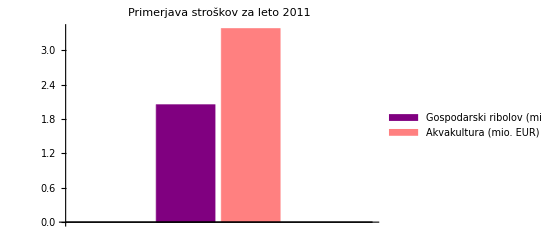
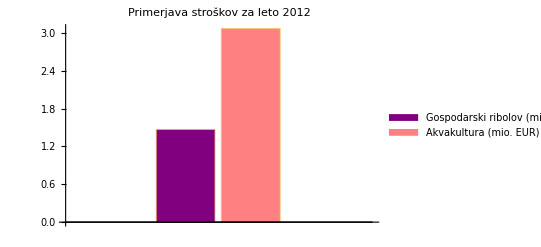
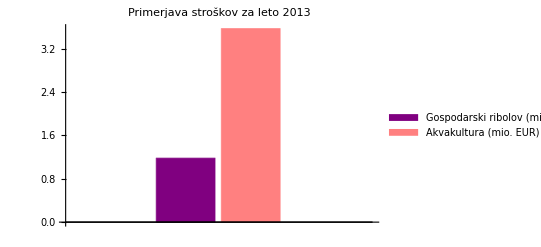
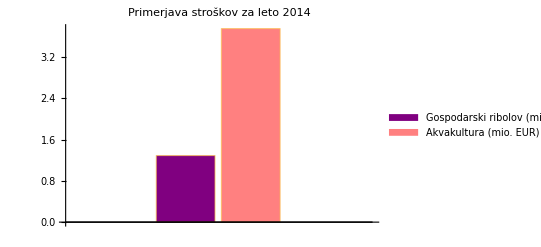
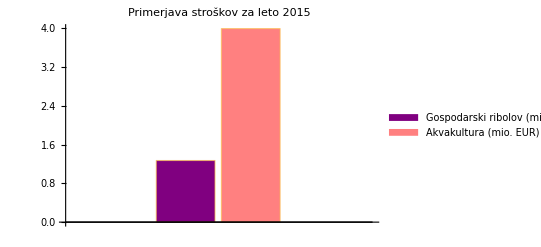
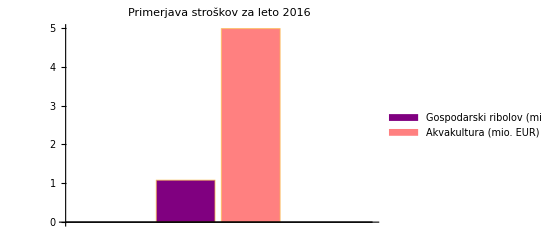
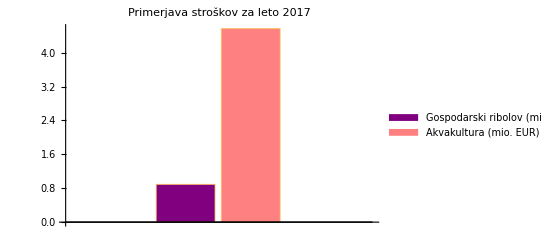
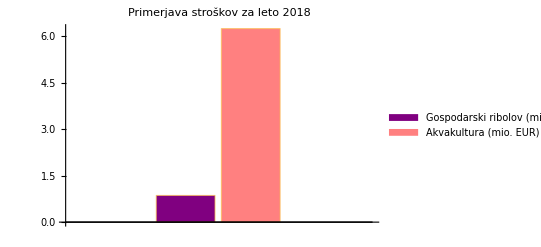
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
prvaTabelaTortnihDiagramov = Table[PieChart[
Part[tabelaTabelPoLetih//Rest,i]//Rest//Query[{1,3}],
ChartLegends->(naslovi//Query[{1,3}]),
PlotLabel-> ("Primerjava
 Gospodarskih ribolovov in Akvakulture
 za leto "  <> ToString[(Part[letnice//Rest,i])] ),
ChartStyle->{Purple,Pink},
(*Epilog->Text[(Part[letnice//Rest,i])],*)
ChartLabels->Placed[(Part[tabelaTabelPoLetih//Rest,i]//Rest//Query[{1,3}]),"RadialCallout"]
],{i,1,10}];

drugaTabelaTortnihDiagramov  =Table[BarChart[
Part[tabelaTabelPoLetih//Rest,i]//Rest//Query[{2,4}],
ChartLegends->(naslovi//Query[{2,4}]),
PlotLabel-> ("Primerjava stroškov
 za leto "  <> ToString[(Part[letnice//Rest,i])] ),
ChartStyle->{Purple,Pink},
(*Epilog->Text[(Part[letnice//Rest,i])],*)
LabelingFunction->(Placed[Panel[#1,FrameMargins->0],Automatic]&)
],{i,1,10}];


(*Do[Print[Part[prvaTabelaTortnihDiagramov,a]],{a,1,Length[prvaTabelaTortnihDiagramov]}]*)
(*Do[Print[Part[drugaTabelaTortnihDiagramov,a]],{a,1,Length[drugaTabelaTortnihDiagramov]}]*)
Table[{Part[prvaTabelaTortnihDiagramov,z],Part[drugaTabelaTortnihDiagramov,z]},{z,1,Length[prvaTabelaTortnihDiagramov]}]
```